# QFT compilation on Delft’s Silicon device

Connectivity of this device

```mathematica
Graph[Table[j->j+1,{j,0,4}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

Set the default configuration of the device

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

## Modules

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
(*Test for the variety of the initial states *)
checkVariation[dev_,unitary_,ntrainstates_,unitaryspace_:{}]:=Module[{conf,a},
conf=DefaultConfig[dev,unitary,ntrainstates,unitaryspace];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
(*Print[i,":",a];*)
ToString[Reverse@Sort[Length/@a]]
]

checkedConf[dev_,unitary_,ntrainstates_,unitaryspace_:{}]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates,unitaryspace];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]

SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_,list_]:=Module[{nansatz,simpncirc,fdist,ρ,qubits,ancillas,bells,ψ,uqubits,time,results,sdate},
sdate=Date[];
results=CircuitSynthesis[qubitsnum,conf];
time=DateDifference[sdate,Date[],"Minutes"];
{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}=results;
AppendTo[list,{conf,time,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}];

nansatz=noisyAnsatz[ansatz/.θvars,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
(* Fidelity distance *)
ρ=CreateDensityQureg[qubitsnum*2];
ψ=CreateQureg[qubitsnum*2];
uqubits=Range[0,-1+IntegerPart[Log2@Length@unitary]];
qubits=Range[0,qubitsnum-1];
ancillas=Range[qubitsnum,qubitsnum*2-1];
bells=Flatten[{Subscript[H, #[[1]]],Subscript[C, #[[1]]][Subscript[X, #[[2]]]]}&/@(Transpose[{qubits,ancillas}])];
ApplyCircuit[ρ,bells];
ApplyCircuit[ψ,bells];
ApplyCircuit[ρ,{Subscript[U, Sequence@@uqubits][ConjugateTranspose@unitary]}];
ApplyCircuit[ρ,simpncirc];

fdist=1-CalcFidelity[ρ,ψ];
DestroyQureg[ρ];
DestroyQureg[ψ];

Print["simulation time:",time,"; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[ansatz,qubitsnum];
Print["cost:",Elist[[-1]]];
Print["dist_fid=",fdist];
]
```

## Noiseless: 6

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->10^5,
(* T2* *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* If true, then the noise model uses T2s otherwise T2 *)
DDActive->True,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(*rabi frequencies on single rotations; random guess *)
RabiFreq-><|0->8,1->8,2->8,3->7,4->5,5->4|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->False,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,0},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
(* obtained from a simple optimisation via bell state fidelity *)
FidCZ-><|0->0.9526707113340579,1->0.9395929490898237,2->0.9484194291327452,3->0.9850519102118337,4->0.9663173858117854|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0,0},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2 *)
ExchangeRotOn->False,
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff->False,

(* Single readout fidelity and duration of the edge qubits, ie 01 and 56 *)
FidRead->1,
DurRead->10,
RepeatRead->2
};
```

Some test to check the device

```mathematica
ρ=CreateDensityQureg[6];
ψ=CreateQureg[6];
```

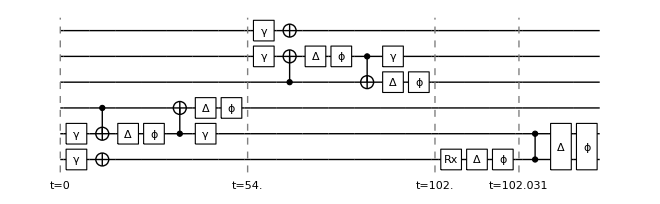

1.

```mathematica
SetQuregMatrix[ρ,RandomMixState[6]];
noisycirc=GetNoisyForm[{Subscript[Init, 0,1,2],Subscript[Init, 3,4,5],Subscript[Rx, 0][π/2],Subscript[C, 0][Subscript[Z, 1]]},SiliconDelft[]];
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
DrawCircuit@noisycirc
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 0],Subscript[X, 5],Subscript[Rx, 0][π/2],Subscript[C, 0][Subscript[Z, 1]]}];
CalcFidelity[ρ,ψ]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=SiliconDelft[];
```

```mathematica
DestroyAllQuregs[];
conf=checkedConf[dev,unitary,5,{3,4,5}];
sidelftclean={};
```

Compilation with automatically generated ansatz at Tue 20 Sep 2022 15:18:46

@cycle1:Tue 20 Sep 2022 15:23:49, fev:237, <E>: 0.10971633361921533 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 1, 90}

I'm slowing down @cycle 2

@cycle2:Tue 20 Sep 2022 15:25:38, fev:306, <E>: 0.10971633361921533 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 11, 0, 1, 124}

@cycle3:Tue 20 Sep 2022 15:46:37, fev:937, <E>: 0.06574975864454212 nansatz: 29 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 6, 206}

@cycle4:Tue 20 Sep 2022 16:14:28, fev:1576, <E>: 0.010996738336422323 nansatz: 36 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 8, 272}

I'm slowing down @cycle 5

@cycle5:Tue 20 Sep 2022 16:24:44, fev:1746, <E>: 0.010996738336422323 nansatz: 36 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 8, 332}

@cycle6:Tue 20 Sep 2022 17:34:45, fev:2773, <E>: 3.693297279355745e-6 nansatz: 38 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 13, 444}

I'm slowing down @cycle 7

@cycle7:Tue 20 Sep 2022 18:41:42, fev:3425, <E>: 3.693297279355745e-6 nansatz: 38 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 13, 519}

I'm slowing down @cycle 8

@cycle8:Tue 20 Sep 2022 19:14:04, fev:3746, <E>: 3.693297279355745e-6 nansatz: 38 merged-smallθ-metric-bf-gmerged: {0, 54, 0, 13, 600}

compile time:2040.21 minutes; total iterations 3843

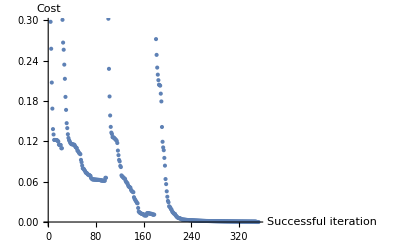

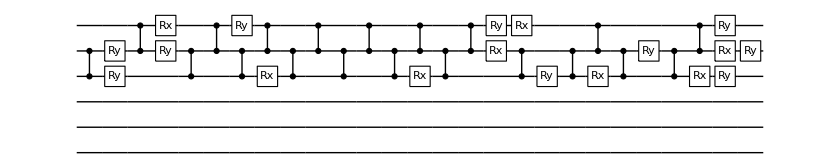

prob(0):<|3→0.333332,4→0.333334,5→0.333334|>

dist_fid=0.999452

Compilation with automatically generated ansatz at Tue 20 Sep 2022 19:18:24

@cycle1:Wed 21 Sep 2022 00:13:08, fev:1963, <E>: 0.000017871702039262694 nansatz: 45 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 12, 392}

I'm slowing down @cycle 2

@cycle2:Wed 21 Sep 2022 00:57:05, fev:2373, <E>: 0.000017871702039262694 nansatz: 45 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 12, 486}

I'm slowing down @cycle 3

@cycle3:Wed 21 Sep 2022 02:47:21, fev:2876, <E>: 0.000017871702039262694 nansatz: 45 merged-smallθ-metric-bf-gmerged: {0, 57, 0, 12, 688}

compile time:2777.02 minutes; total iterations 3000

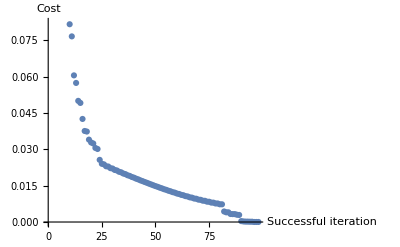

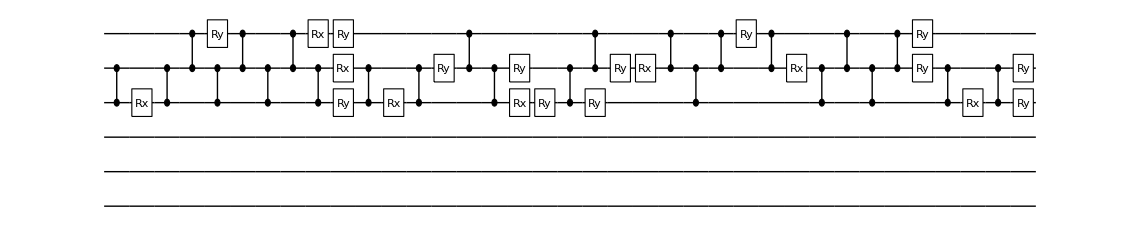

prob(0):<|3→0.333331,4→0.333335,5→0.333335|>

dist_fid=0.999442

Compilation with automatically generated ansatz at Wed 21 Sep 2022 02:52:15

$Aborted

```mathematica
Table[
CompileCirc[conf,unitary,6,sidelftclean]
,{3}]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
```

Use the parameter shift

Compilation with automatically generated ansatz at Wed 21 Sep 2022 12:14:47

@cycle1:Wed 21 Sep 2022 12:53:15, fev:2881, <E>: 0.08478223922086343 nansatz: 20 merged-smallθ-metric-bf-gmerged: {0, 7, 0, 2, 81}

@cycle2:Wed 21 Sep 2022 13:18:46, fev:4316, <E>: 0.0846123499266929 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 10, 0, 4, 118}

@cycle3:Wed 21 Sep 2022 14:00:49, fev:6224, <E>: 0.008938627884143768 nansatz: 32 merged-smallθ-metric-bf-gmerged: {1, 21, 0, 4, 154}

@cycle4:Wed 21 Sep 2022 14:33:27, fev:7677, <E>: 1.5071275042077837e-6 nansatz: 33 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 4, 192}

I'm slowing down @cycle 5

@cycle5:Wed 21 Sep 2022 14:53:21, fev:8452, <E>: 1.5071275042077837e-6 nansatz: 33 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 4, 218}

I'm slowing down @cycle 6

@cycle6:Wed 21 Sep 2022 15:50:38, fev:10159, <E>: 1.5071275042077837e-6 nansatz: 33 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 4, 276}

simulation time:250.617 min; total iterations 12035

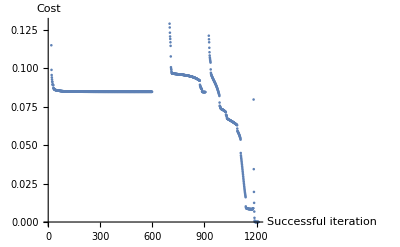

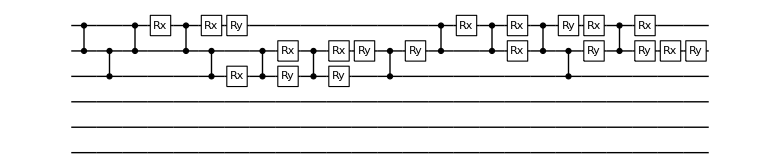

cost:1.50713×10^-6

dist_fid=0.999448

Compilation with automatically generated ansatz at Wed 21 Sep 2022 16:25:26

$Aborted

```mathematica
Table[
DestroyAllQuregs[];
dev=SiliconDelft[];
conf=checkedConf[dev,unitary,5,{3,4,5}];
conf["grad"]="GPS";
CompileCirc[conf,unitary,6,sidelftclean]
,{3}]
```

Parameter shift has a similar performance as the natural gradient. But twice as faster.

## Noiseless: 3

#### Device, check

```mathematica
Options[SiliconDelft]={
qubitsNum->3,
(*average of T1*)
T1->10^5,
(* T2* *)
T2s-><|0-> 3.7,1-> 5.9,2-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0-> 37.2,1-> 44.7,2-> 26.7|>,
(* If true, then the noise model uses T2s otherwise T2 *)
DDActive->True,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0-> 16.1*10^3,1-> 15.9*10^3,2-> 15.69*10^3|>,
(*rabi frequencies on single rotations; random guess *)
RabiFreq-><|0->7,1->5,2->4|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->False,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0-> 0.9988,1-> 0.9991,2-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,0},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0-> 9.8,1-> 5.4|>,
(* obtained from a simple optimisation via bell state fidelity *)
FidCZ-><|0->0.9850519102118337,1->0.9663173858117854|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0,0},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2 *)
ExchangeRotOn->False,
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff->False,

(* Single readout fidelity and duration of the edge qubits, ie 01 and 56 *)
FidRead->1,
DurRead->10,
RepeatRead->2
};
```

Some test to check the device

```mathematica
ρ=CreateDensityQureg[3];
ψ=CreateQureg[3];
```

{{0,{Damp_0[1],X_0,Damp_1[1],C_2[X_1],Depol_1[0],Deph_1[0],C_1[X_2],Depol_2[0],Deph_2[0],Damp_1[1]},{}},{37.5,{Rx_0[π/2],Depol_0[0],Deph_0[0]},{}},{37.5357,{C_1[Z_2],Depol_(1,2)[0],Deph_(1,2)[0]},{}}}

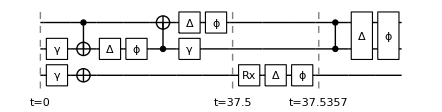

1.

```mathematica
SetQuregMatrix[ρ,RandomMixState[3]];
noisycirc=InsertCircuitNoise[List/@{Subscript[Init, 0,1,2],Subscript[Rx, 0][π/2],Subscript[C, 1][Subscript[Z, 2]]},SiliconDelft[]]
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
DrawCircuit@noisycirc
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 0],Subscript[Rx, 0][π/2],Subscript[C, 1][Subscript[Z, 2]]}];
CalcFidelity[ρ,ψ]
```

#### Trial 1: using Tyson’s derivs func

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=SiliconDelft[];
```

```mathematica
DestroyAllQuregs[];
conf=checkedConf[dev,unitary,5,{0,1,2}];
```

```mathematica
CircuitSynthesis[3,conf]
```

Compilation with automatically generated ansatz at Wed 12 Oct 2022 02:19:32

@cycle1:Wed 12 Oct 2022 02:20:13, fev:325, <E>: 0.21361831873800843 nansatz: 12 merged-smallθ-metric-bf-gmerged: {0, 5, 0, 8, 45}

@cycle2:Wed 12 Oct 2022 02:20:42, fev:573, <E>: 0.04435080444688418 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 8, 66}

I'm slowing down @cycle 3

@cycle3:Wed 12 Oct 2022 02:20:50, fev:635, <E>: 0.04435080444688418 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 12, 0, 8, 92}

@cycle4:Wed 12 Oct 2022 02:22:02, fev:1006, <E>: 0.024478670223753263 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 20, 0, 10, 133}

{{1.10488,1.04363,0.844361,0.603937,0.519299,0.48026,0.464285,0.445768,0.358413,0.333321,0.316112,0.286313,0.258221,0.245665,0.245618,0.245618,0.213618,0.213618,0.363622,0.310309,0.182395,0.120401,0.109463,0.10909,0.10909,0.0489183,0.0453771,0.0453229,0.0453229,0.0453141,0.0452732,0.0445047,0.0445047,0.044442,0.0443983,0.0443983,0.0443595,0.0443595,0.0443508,0.115144,0.101866,0.0951071,0.0530958,0.0414717,0.0341613,0.0317435,0.0276114,0.0257902,0.0257161,0.0256536,0.025456,0.0245014,0.024448,0.0244469,0.0244469,0.0244787,0.0244787,0.168043,0.0882947,0.0320649,0.0228318,0.0215062,0.0208935,0.0204922,0.0202519,0.0201069,0.0199607,0.0198076,0.0197117,0.0192543,0.0190276,0.0188584,0.0187816,0.0183436,0.0183007,0.0180576,0.0160666,0.0126197,0.0109425,0.00956602,0.00870668,0.005445,0.00348776,0.0030712,0.00216482,0.0013437,0.00120567,0.000897101,0.000623951,0.000557317,0.000493677,0.000443269,0.000395483,0.000357176,0.00031816,0.000284436,0.0000908277,0.0000656904,0.0000526401,0.0000481187,0.0000404703,0.0000344782,0.000024735,0.0000152982,0.0000139383,0.0000114556,0.000010027,7.99079×10^-6,6.84977×10^-6,5.92067×10^-6,5.36221×10^-6,4.72671×10^-6,4.23827×10^-6,1.01333×10^-6,4.21724×10^-8,5.3111×10^-9,2.42975×10^-9,1.45767×10^-9,1.04105×10^-9,7.26641×10^-10,5.64892×10^-10,4.51088×10^-10,1.19858×10^-10,1.02364×10^-10,1.02364×10^-10,7.19618×10^-11,7.16366×10^-11,5.99302×10^-11,5.99302×10^-11,3.14193×10^-11,3.14193×10^-11,1.88505×10^-11,2.30616×10^-13},{Ry_0[θ_55],Ry_2[θ_57],Rx_0[θ_58],SWAP_(1,2),C_0[Ph_1[θ_37]],SWAP_(1,2),Ry_0[θ_1],Rx_2[θ_9],C_0[Ph_1[θ_4]],Ry_0[θ_25],SWAP_(1,2),Rx_0[θ_27],Rx_1[θ_15],Ry_0[θ_62],SWAP_(1,2),Rx_0[θ_65],Rx_1[θ_49],Ry_0[θ_68],Ry_1[θ_50],C_1[Ph_2[θ_63]],Ry_2[θ_66],Rx_2[θ_67]},<|θ_1→-3.14159,θ_4→1.5708,θ_9→-4.71239,θ_15→1.5708,θ_25→3.35824,θ_27→3.1416,θ_37→-1.5708,θ_49→-2.35619,θ_50→-1.5708,θ_55→1.57079,θ_57→-1.64408×10^-6,θ_58→5.61279×10^-6,θ_62→0.369852,θ_63→-0.785398,θ_65→-9.41974×10^-7,θ_66→-1.5708,θ_67→1.57079,θ_68→-0.153207|>,Circuit within target precision is found,5,1710,{3},<|ansatz→{{},{Ry_0[θ_1],Rx_2[θ_9],C_0[Ph_1[θ_4]],Rx_1[θ_7],Rx_0[θ_23],SWAP_(1,2),Ry_0[θ_25],Ry_1[θ_11],Rx_0[θ_27],Rx_1[θ_15],SWAP_(1,2),Ry_1[θ_18]},{SWAP_(1,2),Ry_0[θ_33],C_0[Ph_1[θ_37]],SWAP_(1,2),Ry_0[θ_1],Rx_2[θ_9],C_0[Ph_1[θ_4]],Rx_1[θ_7],Ry_0[θ_25],SWAP_(1,2),Rx_0[θ_27],Ry_1[θ_11],Rx_1[θ_15],SWAP_(1,2),Ry_1[θ_18]},{Ry_0[θ_40],SWAP_(1,2),C_0[Ph_1[θ_37]],SWAP_(1,2),Ry_0[θ_1],Rx_2[θ_9],C_0[Ph_1[θ_4]],Rx_1[θ_7],Ry_0[θ_25],SWAP_(1,2),Rx_0[θ_27],Ry_1[θ_11],Rx_1[θ_15],SWAP_(1,2),C_1[Ph_2[θ_47]],Rx_2[θ_48],Rx_1[θ_49],Ry_1[θ_50]},{Rx_0[θ_54],Rx_2[θ_56],Ry_0[θ_55],Ry_2[θ_57],Rx_0[θ_58],C_1[Ph_2[θ_60]],Ry_0[θ_59],SWAP_(1,2),C_0[Ph_1[θ_37]],SWAP_(1,2),Ry_0[θ_1],Rx_2[θ_9],C_0[Ph_1[θ_4]],Rx_1[θ_7],Ry_0[θ_25],SWAP_(1,2),Rx_0[θ_27],Ry_1[θ_11],Ry_0[θ_62],Rx_1[θ_15],Rx_0[θ_65],SWAP_(1,2),Ry_0[θ_68],C_1[Ph_2[θ_47]],Rx_0[θ_69],Rx_2[θ_48],Rx_1[θ_49],Ry_1[θ_50],C_1[Ph_2[θ_63]],Ry_2[θ_66],Rx_2[θ_67]},{Ry_0[θ_55],Ry_2[θ_57],Rx_0[θ_58],SWAP_(1,2),C_0[Ph_1[θ_37]],SWAP_(1,2),Ry_0[θ_1],Rx_2[θ_9],C_0[Ph_1[θ_4]],Ry_0[θ_25],SWAP_(1,2),Rx_0[θ_27],Rx_1[θ_15],Ry_0[θ_62],SWAP_(1,2),Rx_0[θ_65],Rx_1[θ_49],Ry_0[θ_68],Ry_1[θ_50],C_1[Ph_2[θ_63]],Ry_2[θ_66],Rx_2[θ_67]}},θvars→{<||>,<|θ_1→-1.56768,θ_4→1.44756,θ_7→3.50763,θ_9→-3.20638,θ_11→-1.57495,θ_15→1.14966,θ_18→-1.55383,θ_23→1.58112,θ_25→2.16842,θ_27→4.68987|>,<|θ_1→-3.13825,θ_4→1.57496,θ_7→3.53403,θ_9→-3.13795,θ_11→-1.57165,θ_15→1.91937,θ_18→-1.57263,θ_25→3.1401,θ_27→3.15409,θ_33→1.5621,θ_37→-1.6035|>,<|θ_1→-3.13384,θ_4→1.53763,θ_7→4.26229,θ_9→-3.9358,θ_11→-1.56172,θ_15→2.78912,θ_25→3.1371,θ_27→3.14504,θ_37→-1.54278,θ_40→1.5669,θ_47→-1.16807,θ_48→-0.978248,θ_49→-0.589969,θ_50→-1.07431|>,<|θ_1→-3.1416,θ_4→1.5708,θ_7→4.2782,θ_9→-4.71239,θ_11→-1.66518,θ_15→3.24405,θ_25→3.39463,θ_27→2.71815,θ_37→-1.5708,θ_47→0.0000234836,θ_48→-1.67325,θ_49→-0.351209,θ_50→-1.57081,θ_54→-0.200321,θ_55→-0.685863,θ_56→-6.42066×10^-8,θ_57→-1.31399×10^-6,θ_58→-3.85942×10^-6,θ_59→2.25666,θ_60→3.08156×10^-6,θ_62→0.656844,θ_63→-0.785408,θ_65→0.23444,θ_66→-1.57082,θ_67→-0.0943932,θ_68→-0.354335,θ_69→0.190198|>,<|θ_1→-3.14159,θ_4→1.5708,θ_9→-4.71239,θ_15→1.5708,θ_25→3.35824,θ_27→3.1416,θ_37→-1.5708,θ_49→-2.35619,θ_50→-1.5708,θ_55→1.57079,θ_57→-1.64408×10^-6,θ_58→5.61279×10^-6,θ_62→0.369852,θ_63→-0.785398,θ_65→-9.41974×10^-7,θ_66→-1.5708,θ_67→1.57079,θ_68→-0.153207|>},E→{1.10488,0.213618,0.0443508,0.0244787,1.88505×10^-11,2.30616×10^-13},idx→{1,29,38,54,70,70}|>,<|0→0.337399,1→0.330912,2→0.33169|>,-Graphics-,0,27,2,10}

```mathematica
res[[1,-1]]
```

2.30616×10^-13

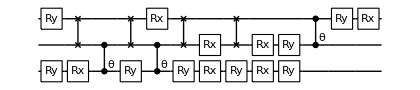

```mathematica
DrawCircuit[res[[2]],3]
```

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
```

```mathematica
res[[2]]/.Subscript[θ, _]:>θ
```

{Ry_0[θ],Ry_2[θ],Rx_0[θ],SWAP_(1,2),C_0[Ph_1[θ]],SWAP_(1,2),Ry_0[θ],Rx_2[θ],C_0[Ph_1[θ]],Ry_0[θ],SWAP_(1,2),Rx_0[θ],Rx_1[θ],Ry_0[θ],SWAP_(1,2),Rx_0[θ],Rx_1[θ],Ry_0[θ],Ry_1[θ],C_1[Ph_2[θ]],Ry_2[θ],Rx_2[θ]}

#### Trial 2: trying out numerics derivs

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=SiliconDelft[];
```

```mathematica
DestroyAllQuregs[];
conf=checkedConf[dev,unitary,5,{0,1,2}];
(*conf["fixansatz"]={Subscript[Ry, 0][θ],Subscript[Ry, 2][θ],Subscript[Rx, 0][θ],Subscript[SWAP, 1,2],Subscript[C, 0][Subscript[Ph, 1][θ]],Subscript[SWAP, 1,2],Subscript[Ry, 0][θ],Subscript[Rx, 2][θ],Subscript[C, 0][Subscript[Ph, 1][θ]],Subscript[Ry, 0][θ],Subscript[SWAP, 1,2],Subscript[Rx, 1][θ],Subscript[SWAP, 1,2],Subscript[Rx, 1][θ],Subscript[Ry, 0][θ],Subscript[Ry, 1][θ],Subscript[C, 1][Subscript[Ph, 2][θ]],Subscript[Ry, 2][θ],Subscript[Rx, 2][θ]};*)
conf["grad"]="NGAN";
conf["greedθ"]=5;
```

```mathematica
Table[CircuitSynthesis[3,conf],{1}]
```

Compilation with automatically generated ansatz at Wed 12 Oct 2022 21:21:26

@cycle1:Wed 12 Oct 2022 21:22:32, fev:502, <E>: 0.17677343156209643 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 1, 0, 0, 59}

@cycle2:Wed 12 Oct 2022 21:23:55, fev:1109, <E>: 0.12190220850776523 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 2, 0, 6, 84}

@cycle3:Wed 12 Oct 2022 21:24:45, fev:1485, <E>: 0.0759559110886462 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 3, 0, 6, 106}

@cycle4:Wed 12 Oct 2022 21:27:00, fev:2221, <E>: 0.06537852746447624 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 6, 0, 9, 119}

@cycle5:Wed 12 Oct 2022 21:28:10, fev:2728, <E>: 1.9921915731524464e-6 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 9, 141}

I'm slowing down @cycle 6

@cycle6:Wed 12 Oct 2022 21:28:37, fev:2925, <E>: 1.9921915731524464e-6 nansatz: 16 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 9, 157}

{{12.6989 min,{1.01179,0.83906,0.769928,0.62622,0.462344,0.365384,0.254992,0.24967,0.238023,0.200944,0.196044,0.179605,0.179148,0.179105,0.179105,0.176773,0.176773,0.447291,0.283921,0.190539,0.147586,0.14722,0.14722,0.147217,0.121902,0.121902,0.231564,0.116898,0.0758451,0.0758451,0.0759559,0.0759559,0.127663,0.10834,0.0953503,0.0761152,0.066224,0.0658661,0.0658661,0.0653785,0.0653785,0.140699,0.0574041,0.0206872,0.0121634,0.00543011,0.00185261,0.00139241,0.000980605,0.000636476,0.000601598,0.000309537,0.000299318,0.000243625,0.000242889,0.000193668,0.000193668,0.0000384426,0.0000227065,0.0000227065,2.9433×10^-6,1.99219×10^-6,1.99219×10^-6,0.0557199,0.00982407,0.00329975,0.00129993,0.000409894,0.000206577,0.0000963589,0.0000428933,0.0000236068,0.0000101648,5.66861×10^-6,2.32473×10^-6,1.19529×10^-6,5.13643×10^-7,2.09227×10^-7,9.87533×10^-8,2.48821×10^-8,1.20898×10^-8,5.82071×10^-9,1.34575×10^-9,2.17904×10^-11,2.17904×10^-11,1.8839×10^-12,3.85547×10^-13},{Ry_2[θ_67],Rx_0[θ_69],Rx_2[θ_68],Ry_0[θ_70],C_0[Ph_1[θ_73]],SWAP_(1,2),C_0[Ph_1[θ_74]],SWAP_(1,2),C_0[Ph_1[θ_75]],Rx_2[θ_78],Ry_2[θ_79],Ry_1[θ_80],Rx_0[θ_77],Ry_0[θ_32],Rx_0[θ_61],C_0[Ph_1[θ_15]],Rx_0[θ_21],Rx_1[θ_20],C_0[Ph_1[θ_24]],Rx_1[θ_49],SWAP_(1,2),C_0[Ph_1[θ_39]],C_1[Ph_2[θ_65]],Rx_0[θ_30],Ry_1[θ_26],Rx_1[θ_55],SWAP_(1,2)},<|θ_15→3.14159,θ_20→-2.3562,θ_21→-3.14159,θ_24→-3.1416,θ_26→1.5708,θ_30→3.14159,θ_32→1.96659,θ_39→-1.5708,θ_49→-2.35619,θ_55→-1.5708,θ_61→-2.91846,θ_65→0.785397,θ_67→0.37466,θ_68→0.423281,θ_69→0.298352,θ_70→0.451441,θ_73→0.0657769,θ_74→4.59408×10^-7,θ_75→-0.0657809,θ_77→-2.60963,θ_78→-0.423282,θ_79→-0.374658,θ_80→-1.5708|>,Circuit within target precision is found,7,4057,{6},<|ansatz→{{},{Rx_0[θ_1],Ry_2[θ_2],Ry_1[θ_5],Rx_2[θ_9],C_0[Ph_1[θ_7]],Ry_2[θ_12],Rx_0[θ_8],Rx_1[θ_11],Rx_2[θ_22],C_0[Ph_1[θ_15]],Ry_2[θ_27],Rx_1[θ_20],Rx_0[θ_21],C_0[Ph_1[θ_24]],Rx_1[θ_25],Rx_0[θ_30],Ry_1[θ_26]},{SWAP_(1,2),Rx_0[θ_1],Ry_2[θ_2],Ry_1[θ_5],Ry_0[θ_32],Rx_2[θ_9],Rx_0[θ_33],Ry_2[θ_27],C_0[Ph_1[θ_15]],Rx_0[θ_21],Rx_1[θ_20],C_0[Ph_1[θ_24]],Rx_1[θ_25],SWAP_(1,2),C_0[Ph_1[θ_39]],Rx_0[θ_30],Ry_1[θ_26]},{SWAP_(1,2),Rx_0[θ_1],Ry_0[θ_32],Ry_1[θ_41],Ry_2[θ_2],Rx_0[θ_46],Rx_2[θ_9],Ry_0[θ_48],Ry_2[θ_47],C_0[Ph_1[θ_15]],Rx_0[θ_21],Rx_1[θ_20],C_0[Ph_1[θ_24]],Rx_1[θ_49],SWAP_(1,2),C_0[Ph_1[θ_39]],Rx_0[θ_30],Ry_1[θ_26]},{SWAP_(1,2),Rx_0[θ_1],Ry_2[θ_51],Ry_0[θ_32],C_1[Ph_2[θ_53]],Rx_0[θ_46],SWAP_(1,2),Ry_0[θ_48],Ry_1[θ_41],C_0[Ph_1[θ_15]],Rx_0[θ_21],Rx_1[θ_20],C_0[Ph_1[θ_24]],Rx_1[θ_49],SWAP_(1,2),C_0[Ph_1[θ_39]],Rx_0[θ_30],Ry_1[θ_26],C_1[Ph_2[θ_54]],Rx_1[θ_55],Ry_2[θ_56],SWAP_(1,2)},{Rx_0[θ_1],Ry_1[θ_41],Ry_0[θ_32],Rx_0[θ_61],C_0[Ph_1[θ_15]],Rx_0[θ_21],Rx_1[θ_20],C_0[Ph_1[θ_24]],Rx_1[θ_49],SWAP_(1,2),C_0[Ph_1[θ_39]],C_1[Ph_2[θ_65]],Rx_0[θ_30],Ry_1[θ_26],Rx_1[θ_55],SWAP_(1,2)},{Ry_2[θ_67],Rx_0[θ_69],Rx_2[θ_68],Ry_0[θ_70],C_0[Ph_1[θ_73]],SWAP_(1,2),C_0[Ph_1[θ_74]],SWAP_(1,2),C_0[Ph_1[θ_75]],Rx_2[θ_78],Ry_0[θ_76],Ry_2[θ_79],Ry_1[θ_80],Rx_0[θ_77],Ry_0[θ_32],Rx_0[θ_61],C_0[Ph_1[θ_15]],Rx_0[θ_21],Rx_1[θ_20],C_0[Ph_1[θ_24]],Rx_1[θ_49],SWAP_(1,2),C_0[Ph_1[θ_39]],C_1[Ph_2[θ_65]],Rx_0[θ_30],Ry_1[θ_26],Rx_1[θ_55],SWAP_(1,2)},{Ry_2[θ_67],Rx_0[θ_69],Rx_2[θ_68],Ry_0[θ_70],C_0[Ph_1[θ_73]],SWAP_(1,2),C_0[Ph_1[θ_74]],SWAP_(1,2),C_0[Ph_1[θ_75]],Rx_2[θ_78],Ry_2[θ_79],Ry_1[θ_80],Rx_0[θ_77],Ry_0[θ_32],Rx_0[θ_61],C_0[Ph_1[θ_15]],Rx_0[θ_21],Rx_1[θ_20],C_0[Ph_1[θ_24]],Rx_1[θ_49],SWAP_(1,2),C_0[Ph_1[θ_39]],C_1[Ph_2[θ_65]],Rx_0[θ_30],Ry_1[θ_26],Rx_1[θ_55],SWAP_(1,2)}},θvars→{<||>,<|θ_1→-0.660072,θ_2→-0.736001,θ_5→-1.5523,θ_7→-1.42895,θ_8→-3.08309,θ_9→0.556957,θ_11→3.1133,θ_12→2.42121,θ_15→1.59345,θ_20→-1.40857,θ_21→-1.54497,θ_22→-1.74962,θ_24→-1.59848,θ_25→-0.375572,θ_26→1.59851,θ_27→0.350136,θ_30→3.25428|>,<|θ_1→-1.92623,θ_2→1.43997,θ_5→-1.28103,θ_9→-1.35934,θ_15→2.40055,θ_20→-1.8228,θ_21→-3.2751,θ_24→-2.73584,θ_25→-1.42873,θ_26→1.43721,θ_27→-1.6452,θ_30→3.26395,θ_32→1.66063,θ_33→-3.29939,θ_39→-1.8149|>,<|θ_1→-2.0113,θ_2→1.55584,θ_9→-1.32032,θ_15→2.78136,θ_20→-2.24595,θ_21→-3.2975,θ_24→-2.84857,θ_26→1.21657,θ_30→3.20368,θ_32→2.0857,θ_39→-1.67396,θ_41→-1.3765,θ_46→-3.31533,θ_47→-1.56357,θ_48→0.527926,θ_49→-1.79137|>,<|θ_1→-2.10863,θ_15→2.76078,θ_20→-2.45891,θ_21→-3.03264,θ_24→-2.6496,θ_26→1.10746,θ_30→2.9666,θ_32→2.02901,θ_39→-1.66073,θ_41→-0.561551,θ_46→-3.19741,θ_48→0.586667,θ_49→-1.94352,θ_51→-0.831118,θ_53→0.341858,θ_54→0.562947,θ_55→-1.31188,θ_56→-0.51275|>,<|θ_1→-2.35574,θ_15→3.1399,θ_20→-2.35716,θ_21→-3.14011,θ_24→-3.14322,θ_26→1.57129,θ_30→3.14291,θ_32→1.57295,θ_39→-1.57134,θ_41→-1.56989,θ_49→-2.35661,θ_55→-1.57106,θ_61→-3.13856,θ_65→0.784344|>,<|θ_15→3.14159,θ_20→-2.35619,θ_21→-3.14159,θ_24→-3.14159,θ_26→1.5708,θ_30→3.14159,θ_32→1.78409,θ_39→-1.5708,θ_49→-2.3562,θ_55→-1.5708,θ_61→-3.02274,θ_65→0.785398,θ_67→0.378168,θ_68→0.426291,θ_69→0.284489,θ_70→0.655233,θ_73→0.0657786,θ_74→-1.13192×10^-6,θ_75→-0.0657792,θ_76→-0.411507,θ_77→-2.62794,θ_78→-0.426291,θ_79→-0.378167,θ_80→-1.5708|>,<|θ_15→3.14159,θ_20→-2.3562,θ_21→-3.14159,θ_24→-3.1416,θ_26→1.5708,θ_30→3.14159,θ_32→1.96659,θ_39→-1.5708,θ_49→-2.35619,θ_55→-1.5708,θ_61→-2.91846,θ_65→0.785397,θ_67→0.37466,θ_68→0.423281,θ_69→0.298352,θ_70→0.451441,θ_73→0.0657769,θ_74→4.59408×10^-7,θ_75→-0.0657809,θ_77→-2.60963,θ_78→-0.423282,θ_79→-0.374658,θ_80→-1.5708|>},E→{1.01179,0.176773,0.121902,0.0759559,0.0653785,1.99219×10^-6,1.8839×10^-12,3.85547×10^-13},idx→{1,31,40,50,58,67,81,81}|>,<|0→0.333333,1→0.333333,2→0.333334|>,-Graphics-,1,17,0,9}}

```mathematica
res=%;
```

```mathematica
res[[1,2]]
```

{1.01179,0.83906,0.769928,0.62622,0.462344,0.365384,0.254992,0.24967,0.238023,0.200944,0.196044,0.179605,0.179148,0.179105,0.179105,0.176773,0.176773,0.447291,0.283921,0.190539,0.147586,0.14722,0.14722,0.147217,0.121902,0.121902,0.231564,0.116898,0.0758451,0.0758451,0.0759559,0.0759559,0.127663,0.10834,0.0953503,0.0761152,0.066224,0.0658661,0.0658661,0.0653785,0.0653785,0.140699,0.0574041,0.0206872,0.0121634,0.00543011,0.00185261,0.00139241,0.000980605,0.000636476,0.000601598,0.000309537,0.000299318,0.000243625,0.000242889,0.000193668,0.000193668,0.0000384426,0.0000227065,0.0000227065,2.9433×10^-6,1.99219×10^-6,1.99219×10^-6,0.0557199,0.00982407,0.00329975,0.00129993,0.000409894,0.000206577,0.0000963589,0.0000428933,0.0000236068,0.0000101648,5.66861×10^-6,2.32473×10^-6,1.19529×10^-6,5.13643×10^-7,2.09227×10^-7,9.87533×10^-8,2.48821×10^-8,1.20898×10^-8,5.82071×10^-9,1.34575×10^-9,2.17904×10^-11,2.17904×10^-11,1.8839×10^-12,3.85547×10^-13}

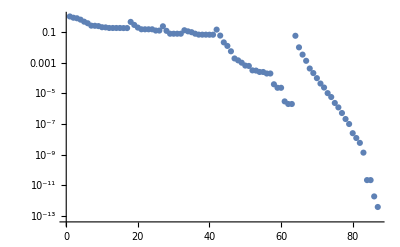

```mathematica
ListLogPlot[res[[1,2]]]
```

```mathematica
{ρ,ρwork}=CreateDensityQuregs[3,2];
trainkey=1;
```

```mathematica
θvars=<|Subscript[θ, 1]->-1.3277616942381314,Subscript[θ, 2]->-1.9350066018938061,Subscript[θ, 3]->-0.7724373478569029,Subscript[θ, 4]->-0.9551435529376101,Subscript[θ, 5]->0.12841152895835664,Subscript[θ, 6]->0.9880065038031374,Subscript[θ, 7]->-1.2570412495795482,Subscript[θ, 8]->0.023426879077275555,Subscript[θ, 9]->0.9555761051305847,Subscript[θ, 10]->1.3939009545654875,Subscript[θ, 11]->-1.1897677279996968,Subscript[θ, 12]->-2.2263746354791842,Subscript[θ, 13]->1.4866870546018116,Subscript[θ, 14]->1.7249612992888173,Subscript[θ, 15]->-1.9538432374818815|>;
ansatz={Subscript[Ry, 0][Subscript[θ, 1]],Subscript[Ry, 2][Subscript[θ, 2]],Subscript[Rx, 0][Subscript[θ, 3]],Subscript[SWAP, 1,2],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 4]]],Subscript[SWAP, 1,2],Subscript[Ry, 0][Subscript[θ, 5]],Subscript[Rx, 2][Subscript[θ, 6]],Subscript[C, 0][Subscript[Ph, 1][Subscript[θ, 7]]],Subscript[Ry, 0][Subscript[θ, 8]],Subscript[SWAP, 1,2],Subscript[Rx, 1][Subscript[θ, 9]],Subscript[SWAP, 1,2],Subscript[Rx, 1][Subscript[θ, 10]],Subscript[Ry, 0][Subscript[θ, 11]],Subscript[Ry, 1][Subscript[θ, 12]],Subscript[C, 1][Subscript[Ph, 2][Subscript[θ, 13]]],Subscript[Ry, 2][Subscript[θ, 14]],Subscript[Rx, 2][Subscript[θ, 15]]};
```

```mathematica
dθ=10^-2;
k=Subscript[θ, 3];
θs={-dθ,0,dθ};

ρms=Table[
θvarst=θvars;
θvarst[k]+=dθ;
CloneQureg[ρ,conf["ρinit"][trainkey]];
ApplyCircuit[ρ,Flatten[{ansatz/.θvarst,conf["undocirc"][trainkey]}]];
GetQuregMatrix[ρ]
,{δ,θs}];
ρdim=Length@ρms[[1]];
```

```mathematica
Table[
datare=Table[{θvars[k]+θs[[j]],Re@ρms[[j]][[r,c]]},{j,Length@θs}]//Chop;
dataim=Table[{θvars[k]+θs[[j]],Im@ρms[[j]][[r,c]]},{j,Length@θs}]//Chop;

fit={
FindFit[datare,const*Sin[a*t],{a,const},t],
FindFit[dataim,const*Sin[a*t],{a,const},t]
};

Chop[(a*const*Cos[a*θvars[k]]/.fit[[1]])+ⅈ (a*const*Cos[a*θvars[k]]/.fit[[2]])]
,{r,ρdim},{c,ρdim}]//MatrixForm
```

(-0.0000436059 | 7.50119×10^-6+9.10382×10^-6 ⅈ | 5.94469×10^-6+0.0000313085 ⅈ | -6.52046×10^-6-4.72362×10^-6 ⅈ | 0.0000209907+0.0000122527 ⅈ | -4.56343×10^-6-5.89433×10^-7 ⅈ | -8.29953×10^-6-2.27585×10^-6 ⅈ | 8.66152×10^-6+3.14447×10^-6 ⅈ
7.50119×10^-6-9.10412×10^-6 ⅈ | -3.19124×10^-6 | -7.55902×10^-6-4.14448×10^-6 ⅈ | 2.10792×10^-6-5.48846×10^-7 ⅈ | -6.1687×10^-6+2.27477×10^-6 ⅈ | 9.08185×10^-7-8.51391×10^-7 ⅈ | 1.90297×10^-6-1.34145×10^-6 ⅈ | -2.1464×10^-6+1.26753×10^-6 ⅈ
5.94469×10^-6-0.0000313075 ⅈ | -7.55902×10^-6+4.14463×10^-6 ⅈ | -0.0000232902 | 4.28024×10^-6-4.03777×10^-6 ⅈ | -0.0000116591+0.0000134007 ⅈ | 1.04535×10^-6-3.19616×10^-6 ⅈ | 2.76558×10^-6-5.64915×10^-6 ⅈ | -3.43833×10^-6+5.78987×10^-6 ⅈ
-6.52046×10^-6+4.72362×10^-6 ⅈ | 2.10792×10^-6+5.48846×10^-7 ⅈ | 4.28024×10^-6+4.03771×10^-6 ⅈ | -1.48661×10^-6 | 4.46602×10^-6-4.41641×10^-7 ⅈ | -7.46237×10^-7+4.06208×10^-7 ⅈ | -1.48756×10^-6+5.58794×10^-7 ⅈ | 1.63571×10^-6-4.68065×10^-7 ⅈ
0.0000209907-0.0000122528 ⅈ | -6.1687×10^-6-2.27491×10^-6 ⅈ | -0.0000116591-0.0000134006 ⅈ | 4.46602×10^-6+4.41641×10^-7 ⅈ | -0.0000135471 | 2.36239×10^-6-9.98538×10^-7 ⅈ | 4.63491×10^-6-1.23677×10^-6 ⅈ | -5.05298×10^-6+9.20215×10^-7 ⅈ
-4.56343×10^-6+5.89433×10^-7 ⅈ | 9.08185×10^-7+8.51553×10^-7 ⅈ | 1.04535×10^-6+3.19625×10^-6 ⅈ | -7.46237×10^-7-4.06208×10^-7 ⅈ | 2.36239×10^-6+9.98599×10^-7 ⅈ | -4.85562×10^-7 | -8.9935×10^-7-1.25984×10^-7 ⅈ | 9.49029×10^-7+2.12002×10^-7 ⅈ
-8.29953×10^-6+2.27572×10^-6 ⅈ | 1.90297×10^-6+1.34148×10^-6 ⅈ | 2.76558×10^-6+5.64915×10^-6 ⅈ | -1.48756×10^-6-5.58794×10^-7 ⅈ | 4.63491×10^-6+1.23669×10^-6 ⅈ | -8.9935×10^-7+1.25984×10^-7 ⅈ | -1.69863×10^-6 | 1.81277×10^-6+1.46468×10^-7 ⅈ
8.66152×10^-6-3.14459×10^-6 ⅈ | -2.1464×10^-6-1.26757×10^-6 ⅈ | -3.43833×10^-6-5.79027×10^-6 ⅈ | 1.63571×10^-6+4.68065×10^-7 ⅈ | -5.05298×10^-6-9.20089×10^-7 ⅈ | 9.49029×10^-7-2.12002×10^-7 ⅈ | 1.81277×10^-6-1.46468×10^-7 ⅈ | -1.94721×10^-6)

```mathematica
Table[Subscript[a, r,c],{r,1,2},{c,0,5}]//MatrixForm
```

(a_(1,0) | a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,0) | a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5))

```mathematica
fit
```

{a→0.00831667+0.0351824 ⅈ,b→-0.141901+0.0335437 ⅈ}

```mathematica
deriv[θvars[k]]/.fit
```

1.49238×10^-14-5.59948×10^-13 ⅈ

```mathematica
data={{-1.3377616942381314,0.03806344511189927+0.15072188911115525 ⅈ},{-1.3277616942381314,0.03806344511189927+0.15072188911115525 ⅈ},{-1.3177616942381314,0.03806344511189927+0.15072188911115525 ⅈ}};
```

```mathematica
data[[All,2]]
```

{0.0380634+0.150722 ⅈ,0.0380634+0.150722 ⅈ,0.0380634+0.150722 ⅈ}

```mathematica
datare=Transpose[{data[[All,1]],Re@data[[All,2]]}]
dataim=Transpose[{data[[All,1]],Im@data[[All,2]]}]
```

{{-1.33776,0.0380634},{-1.32776,0.0380634},{-1.31776,0.0380634}}

{{-1.33776,0.150722},{-1.32776,0.150722},{-1.31776,0.150722}}

```mathematica
fit={
FindFit[datare,c*Sin[a*t],{a,c},t],
FindFit[dataim,c*Sin[a*t],{a,c},t]
}
```

{{a→1.18303,c→-0.0380652},{a→1.18303,c→-0.150729}}

```mathematica
(deriv2[θvars[k]]/.fit[[1]])+ⅈ (deriv2[θvars[k]]/.fit[[2]])
```

-6.68771×10^-7-2.64816×10^-6 ⅈ

```mathematica
deriv2[t_]:=a*c*Cos[a*t]
```

```mathematica
deriv[t_]:=-a*Sin[t]+ⅈ b*Cos[t]
```

```mathematica
res[[1,-1]]
```

2.30616×10^-13

```mathematica
DrawCircuit[res[[2]],3]
```

-Graphics-

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
```

```mathematica
res[[2]]/.Subscript[θ, _]:>θ
```

{Ry_0[θ],Ry_2[θ],Rx_0[θ],SWAP_(1,2),C_0[Ph_1[θ]],SWAP_(1,2),Ry_0[θ],Rx_2[θ],C_0[Ph_1[θ]],Ry_0[θ],SWAP_(1,2),Rx_0[θ],Rx_1[θ],Ry_0[θ],SWAP_(1,2),Rx_0[θ],Rx_1[θ],Ry_0[θ],Ry_1[θ],C_1[Ph_2[θ]],Ry_2[θ],Rx_2[θ]}

## Noisy: 3

#### Device, check

```mathematica
Options[SiliconDelft]={
qubitsNum->3,
(*average of T1*)
T1->10^5,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0-> 37.2,1-> 44.7,2-> 26.7|>,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0-> 16.1*10^3,1-> 15.9*10^3,2-> 15.69*10^3|>,
(*rabi frequencies on single rotations; random guess *)
RabiFreq-><|0->7,1->5,2->4|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->True,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,
(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0-> 0.9988,1-> 0.9991,2-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0-> 9.8,1-> 5.4|>,
(* obtained from a simple optimisation via bell state fidelity *)
FidCZ-><|0->0.9850519102118337,1->0.9663173858117854|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0,1},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2 *)
ExchangeRotOn->True,
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff-><|0->0.02,1-> 0.028|>,

(* Single readout fidelity and duration of the edge qubits, ie 01 and 56 *)
FidRead->0.99,
DurRead->10
};
```

Some test to check the device

```mathematica
ρ=CreateDensityQureg[3];
ψ=CreateQureg[3];
```

{{0,{Damp_0[0.9999],X_0,Damp_1[0.9999],C_2[X_1],Depol_1[0.],Deph_1[0.00135],U_0[{{0.995186-0.0979713 ⅈ,6.96609×10^-15-0.00244928 ⅈ},{6.96609×10^-15-0.00244928 ⅈ,0.995186+0.0979713 ⅈ}}],U_2[{{0.995633+0.093324 ⅈ,-1.08984×10^-17-0.002222 ⅈ},{-1.08984×10^-17-0.002222 ⅈ,0.995633-0.093324 ⅈ}}],C_1[X_2],Depol_2[0.],Deph_2[0.00165],U_0[{{0.99953-0.0306427 ⅈ,8.34736×10^-16-0.000298953 ⅈ},{8.34736×10^-16-0.000298953 ⅈ,0.99953+0.0306427 ⅈ}}],U_1[{{0.99821-0.0597879 ⅈ,5.58564×10^-18-0.00113882 ⅈ},{5.58564×10^-18-0.00113882 ⅈ,0.99821+0.0597879 ⅈ}}],Damp_1[0.99]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.]],Deph_1[0.],Depol_1[0.],Deph_2[0.],Depol_2[0.]}},{37.5,{Rx_0[π/2],Depol_0[0.],Deph_0[0.0018],U_1[{{0.995378+0.0959748 ⅈ,-4.77689×10^-15-0.00335912 ⅈ},{-4.77689×10^-15-0.00335912 ⅈ,0.995378-0.0959748 ⅈ}}],U_2[{{0.998753+0.0469117 ⅈ,-0.0170519+2.38061×10^-14 ⅈ},{-0.0170519+2.38061×10^-14 ⅈ,-0.998753+0.0469117 ⅈ}}]},{C_0[Rz_1[0.]],Deph_0[0.],Depol_0[0.],C_1[Rz_2[0.00031831]],Deph_1[0.000399329],Depol_1[2.67857×10^-7],Deph_2[0.00066836],Depol_2[2.67857×10^-7]}},{37.5357,{C_1[Z_2],Depol_(1,2)[0.],Deph_(1,2)[0.0421033]},{Deph_0[0.00124298],Depol_0[6.94444×10^-7],Deph_1[0.],Depol_1[0.],Deph_2[0.],Depol_2[0.]}}}

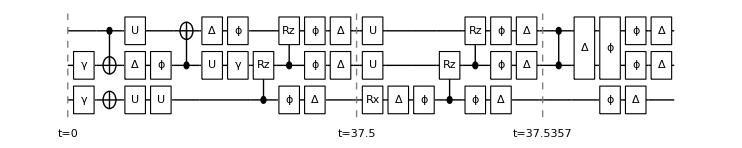

0.991066

```mathematica
SetQuregMatrix[ρ,RandomMixState[3]];
noisycirc=InsertCircuitNoise[List/@{Subscript[Init, 0,1,2],Subscript[Rx, 0][π/2],Subscript[C, 1][Subscript[Z, 2]]},SiliconDelft[]]
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
DrawCircuit@noisycirc
ApplyCircuit[InitZeroState@ψ,{Subscript[X, 0],Subscript[Rx, 0][π/2],Subscript[C, 1][Subscript[Z, 2]]}];
CalcFidelity[ρ,ψ]
```

#### Trial 1

```mathematica
unitary=CalcCircuitMatrix@QFT@3;
dev=SiliconDelft[];
```

```mathematica
DestroyAllQuregs[];
conf=checkedConf[dev,unitary,5,{0,1,2}];
conf["grad"]="NGAN";
```

```mathematica
resn=CircuitSynthesis[3,conf]
```

Compilation with automatically generated ansatz at Wed 12 Oct 2022 21:41:02

$Aborted